This notebook aims to plot the effect of environmental parameters on discount rate and risk aversion during the life of an individual:

we always assume:

at an age t, an individual is characterized by: 

body weight w[t]
production p[w] 
mortality rate m[w]

power functions are assumed for p and m = 

p[w_]:=κ w ^α;
m[w_]:=μ/w^β;

(with  w >= 1)

# Discounting

## Intermediate calculations

These derivations need not be evaluated before generating the plots. They are only here for a better understanding of the method used.

#### Derivation of growth trajectory w[t]

```mathematica
ClearAll["Global`*"]

p[w_]:=κ w ^α

DSolve[{w'[t]==p[w[t]],w[0]==w0},w[t],t]//FullSimplify
```

```mathematica
{{w[t]->(w0^(1-α)+κ (t-t α))^(1/(1-α))}}
```

#### Derivation of ESS adult size wa

Found as the solution of a differential equation

```mathematica
p[w_]:=κ w ^α
m[w_]:=μ/w^β 

mw[w_]:=-μ w^(-1-β) β 
pw[w_]:=κ w^(-1+α) α
(*derivatives of death rate and productivity with regard to w*)


Solve[pw[w]/m[w]-(mw[w] p[w])/m[w]^2==1,w]//FullSimplify
```

#### Derivation of age at maturity ta

Found as the age at which body size = ESS adult size wa

```mathematica
ClearAll["Global`*"]
w[t_]:=(w0^(1-α)+κ (t-t α))^(1/(1-α))
wa:=(κ/m(α+β))^(1/(1-α-β))
Solve[w[t]==wa,t]//FullSimplify
```

```mathematica
{{t->(w0^-α (w0-w0^α (((κ (α+β))/m)^(-1/(-1+α+β)))^(1-α)))/(κ (-1+α))}}
```

#### Derivation of l[t] during growth

```mathematica
ClearAll["Global`*"]

m[w_]:=m w^(-β)

w[t_]:=(w0^(1-α)+κ (t-t α))^(1/(1-α)) (*body Weight during growth*)

l[t]:=Exp[-Integrate[m[w[s]],{s,0,t}]]
```

```mathematica
l[t]//FullSimplify
```

```mathematica
ConditionalExpression[ⅇ^(-(m w0^-α (w0 ((w0^(1-α))^(1/(1-α)))^-β+(-w0+κ t w0^α (-1+α)) ((w0^(1-α)+κ (t-t α))^(1/(1-α)))^-β))/(κ (-1+α+β))),Re[w0^(1-α)/(κ t (-1+α))]>1||Re[w0^(1-α)/(κ t (-1+α))]<0||w0^(1-α)/(κ t (-1+α))∉Reals]
```

```mathematica
(*with α<1 the condition is verified*)
```

#### Derivation of λa: costate at switching age

by definition of the switching age, we have λa=la ; so from the value of l[t] above, we can derive the costate at the switching age

```mathematica
λa=l[ta]; (*co-state at switching age*)
```

#### Derivation of λ[t] during growth

during growth phase the co-state of body weight obeys the following Diff. equation :

```mathematica
ClearAll["Global`*"]

p[w_]:=κ w ^α
m[w_]:=μ w^(-β)

mw[w_]:=-μ w^(-1-β) β 
pw[w_]:=κ w^(-1+α) α
(*derivatives of death rate and productivity with regard to w*)

w[t_]:=(w0^(1-α)+κ (t-t α))^(1/(1-α))

DSolve[{λ'[t]==mw[w[t]]V0-pw[w[t]]λ[t],λ[ta]==λa},λ[t],t]
```

This equation has no analytical solution ; it will be solved numerically

#### Derivation of discount rate δ

During pure reproduction (t>AgeMaturityESS),  discount rate is always exactly equal to the adult mortality rate

```mathematica
ClearAll["Global`*"]

m[w_]:=m w^(-β)
wa:=(κ/m(α+β))^(1/(1-α-β))
m[wa]//FullSimplify
```

```mathematica
m (((κ (α+β))/m)^(-1/(-1+α+β)))^-β
```

During growth, discount rate is given by

```mathematica
δ[t_]:=pw[w[t]]-mw[w[t]] V0/λ[t](*discount rate during growth*)
```

we will use λ[t] obtained numericaly in order to calculate this discount rate

## Plot function (To Evaluate first)

```mathematica
ClearAll["Global`*"]
LHS := Function[{α,β,κ,μ,w0,Tmax}, (*computes the optimal life cycle for the for the given parameters*)
p[w_]:=κ w ^α;
m[w_]:=μ/w^β;
mw[w_]:=-μ w^(-1-β) β ;
pw[w_]:=κ w^(-1+α) α;
w[t_]:=(w0^(1-α)+κ (t-t α))^(1/(1-α)) ;
l[t_]:=ⅇ^(-(μ w0^-α (w0 ((w0^(1-α))^(1/(1-α)))^-β+(-w0+κ t w0^α (-1+α)) ((w0^(1-α)+κ (t-t α))^(1/(1-α)))^-β))/(κ (-1+α+β)));
wa:=(κ/μ(α+β))^(1/(1-α-β));
ta:=(w0^-α (w0-w0^α (((κ (α+β))/μ)^(-1/(-1+α+β)))^(1-α)))/(κ (-1+α));

pa=p[wa];
ma=m[wa];
la=l[ta];

λa=la;

V0=la pa/ma ;

sol=NDSolve[{λ'[t]==-pw[w[t]]λ[t] +  mw[w[t]] V0 ,λ[ta]==λa},λ[t],{t,0,ta}];

δg[t_]:=(pw[w[t]] -  (mw[w[t]] V0)/λ[t])/.sol;

δa[t_]:=ma;

AppendTo[params,{α,β,w0,κ,μ,Tmax}]; (*appends to the list params the parameters values given*)
AppendTo[LifeCycle,{ta,wa,w[t],l[t],{λ[t]/.sol},pw[w[t]],p[w[t]],m[w[t]]}]; 
(*appends to the list LifeCycle the main variables of the optimal life cycle*)
AppendTo[discounting,{δg[t],δa[t]}] 
(*appends to the list discounting the optimal discount rate at each age during growth and reproduction*)
]

PlotEnv :=Function[{parameter,α,β,κ,μ,w0,Tmax}, 
(*generates the plots for the discounting throughout the lifecycle for a range of parameter values*)

Table[LHS[α,β,κ,μ,w0,Tmax],{parameter,int}];
(*use the LHS function to compute the optimal life cycle across a range of a given parameter*)

funcdiscountg=Table[Piecewise[{{discounting[[i,1]],t<LifeCycle[[i,1]]},{Indeterminate,True}}],{i,1,nc}]; (*discount rate during growth for the optimal lifecycles*)

funcdiscounta=Table[Piecewise[{{discounting[[i,2]],t>LifeCycle[[i,1]]},{Indeterminate,True}}],{i,1,nc}]; (*discount rate during reproduction for the optimal lifecycles*)

Pg=Plot[funcdiscountg,{t,0,70}, PlotStyle->Table[ColorData["Rainbow",i/(Length[funcdiscountg]-1)],{i,0,Length[funcdiscountg]-1}],Axes->False,Exclusions->None,Frame->True, PlotRange->All];
(*plot for the discount rate during growth*)
Pa=Plot[funcdiscounta,{t,0,70},PlotStyle->Table[ColorData["Rainbow",i/(Length[funcdiscounta]-1)],{i,0,Length[funcdiscounta]-1}], Exclusions->None];
(*plot for the discount rate during reproduction*)
Show[Pa,Pg,Exclusions->None, AxesOrigin->{0,0},PlotRange->All]
(*combines the two plots on a same graph to cover the whole lifecycle*)
]
```

## Plots

Discounting throughout lifetime

```mathematica
α:=0.6
β:=0.1
κ:=1
μ:=0.1
w0:=1
Tmax:=70
params={};
LifeCycle={};
discounting={};
```

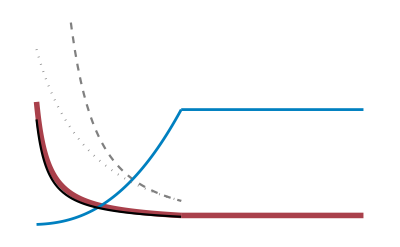

```mathematica
LHS[α,β,κ,μ,w0,Tmax]; (*The function LHS is called to compute the optimal life cycle*)
Pg=Plot[{δg[t],{λ[t]/.sol},w[t]/1000,pw[w[t]],l[t]},{t,0,ta},PlotStyle->{{RGBColor[0.5529411764705883, 0., 0.054901960784313725, 0.75],Thickness[0.01]},{Gray, Dashed},{RGBColor[0., 0.5019607843137255, 0.7529411764705882], Thickness[0.005]},RGBColor[0., 0., 0.],{Gray, Dotted}}];
(*Discount rate during growth*)
Pa=Plot[{wa/1000,ma},{t,ta,Tmax}, PlotStyle->{{RGBColor[0., 0.5019607843137255, 0.7529411764705882],Thickness[0.005]}, {RGBColor[0.5529411764705883, 0., 0.054901960784313725, 0.75],Thickness[0.01]}}];
(*Discount rate during reproduction*)
Show[Pg,Pa,PlotRange->All,Axes->False,Frame->False]
(*combines the two plots on the same graph ---> see Figure 1 in the article text*)
```

Discounting across environments

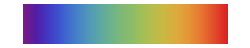

```mathematica
ColorData["Rainbow","Image"]
```

### Effect of α

Evolutionary stable discount rate across a range of values for the α parameter, which captures the productivity of the environment. 
α ∈ [0,1] and higher values mean a more productive environment.

```mathematica
Clear[α]
β:=0.1
κ:=1
μ:=0.1
w0:=1
Tmax:=70
αmin:=0.15 (*lower bound for the range of α values*)
αmax:=0.65 (*upper bound for the range of α values*)
nc:=100 (*number of subdivisions*)
int=Subdivide[αmin,αmax,nc-1];
params={}; (*empty params list for the LHS function*)
LifeCycle={}; (*empty LifeCycle list for the LHS function*)
discounting={}; (*empty discounting list for the lHS function*)
```

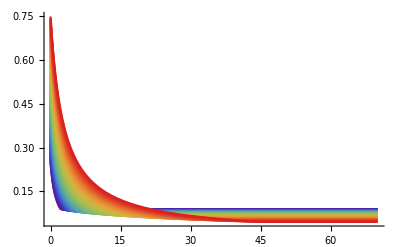

```mathematica
PlotEnv[parameter=α,α,β,κ,μ,w0,Tmax]
```

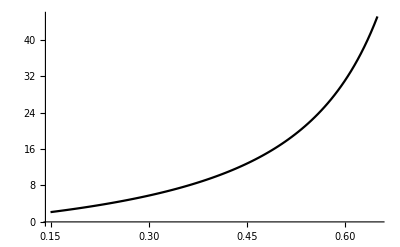

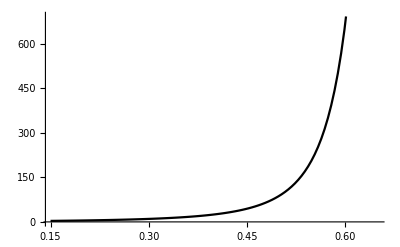

```mathematica
ListLinePlot[Flatten/@Transpose[{params[[1;;, 1]],LifeCycle[[1;;, 1]]}],PlotStyle->Black, TicksStyle->Larger] (*optimal age at maturity for a range of α values*)
ListLinePlot[Flatten/@Transpose[{params[[1;;, 1]],LifeCycle[[1;;, 2]]}],PlotStyle->Black, TicksStyle->Larger](*optimal size at maturity for a range of α values*)
```

### Effect of β

Evolutionary stable discount rate across a range of values for the β parameter, which captures the “safeness” of the environment. 
β  > 0 and higher values mean an environment where it is easier to obtain protections against mortality sources.

```mathematica
Clear[β]
α :=0.5
κ:=1
μ:=0.1
w0:=1
Tmax:=70
βmin:=0.025 (*lower bound for the range of β values*)
βmax:=0.25   (*upper bound for the range of β values*)
nc:=100          (*number of subdivisions*)
int=Subdivide[βmin,βmax,nc-1];
params={};
LifeCycle={};
discounting={};
```

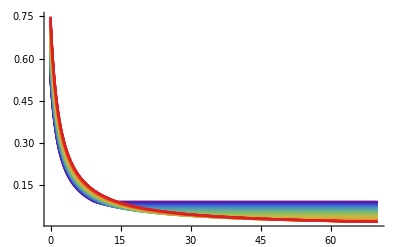

```mathematica
PlotEnv[parameter =β,α,β,κ,μ,w0,Tmax]
```

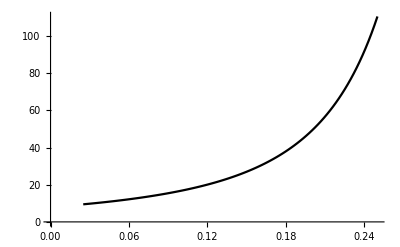

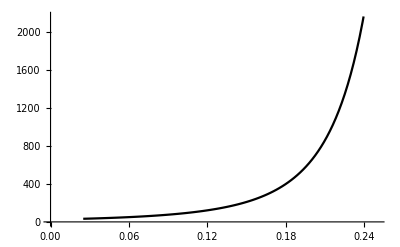

```mathematica
ListLinePlot[Flatten/@Transpose[{params[[1;;, 2]],LifeCycle[[1;;, 1]]}],PlotStyle->Black, TicksStyle->Larger] (*optimal age at maturity for a range of β values*)
ListLinePlot[Flatten/@Transpose[{params[[1;;, 2]],LifeCycle[[1;;, 2]]}],PlotStyle->Black, TicksStyle->Larger](*optimal size at maturity for a range of β values*)
```

### Effect of w0

Evolutionary stable discount rate across a range of values for the w0 parameter, which is individuals’ body weight at birth (w0 ≥ 1).

```mathematica
Clear[w0]
α :=0.5;
β:=0.1;
κ:=1;
μ:=0.1;
Tmax:=70;
w0min:=1;   (*lower bound for the range of w0 values*)
w0max:=50;(*upper bound for the range of w0 values*)
nc:=250;     (*number of subdivisions*)
int=Subdivide[w0min,w0max,nc-1];
params={};
LifeCycle={};
discounting={};
```

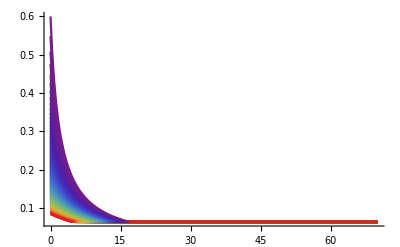

```mathematica
PlotEnv[parameter =w0,α,β,κ,μ,w0,Tmax]
```

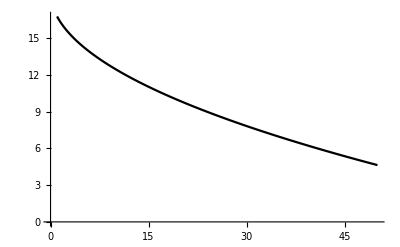

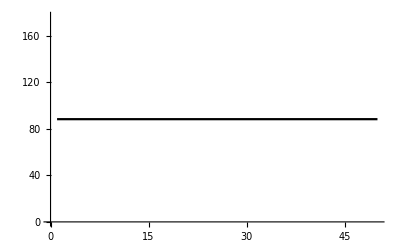

```mathematica
ListLinePlot[Flatten/@Transpose[{params[[1;;, 3]],LifeCycle[[1;;, 1]]}],PlotStyle->Black, TicksStyle->Larger](*optimal age at maturity for a range of w0 values*)
ListLinePlot[Flatten/@Transpose[{params[[1;;, 3]],LifeCycle[[1;;, 2]]}],PlotStyle->Black, TicksStyle->Larger](*optimal size at maturity for a range of w0 values*)
```

# Risk aversion

We give a “bonus” δ (which can actually be positive or negative) to individuals at a specific age tb, we calculate the fitness obtained, and the degree of risk aversion at age tb is given by the opposite of the second order derivative of this fitness function in function of the size of the bonus δ.

(note that in the article text, the bonus is written ϵ instead of δ)

## Intermediate calculations

These derivations need not be evaluated before generating the plots. They are only here for a better understanding of the method used.

#### Derivation of w2[t] = growth trajectory after the bonus

```mathematica
ClearAll["Global`*"]

p[w_]:=κ w ^α;
m[w_]:=μ/w^β;

wa:=(κ/μ(α+β))^(1/(1-α-β))(*Adult Weight at ESS*);

w1[t_]:=(w0^(1-α)+κ (t-t α))^(1/(1-α)) (*Body Weight during growth until tb*);
```

after the bonus we have w[tb]=w[tb]+δ

```mathematica
DSolve[{w'[t]==p[w[t]],w[tb]==δ+(w0^(1-α)+κ (tb-tb α))^(1/(1-α))},w[t],t]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{w[t]→(1/(1-α)(-1+α) (t (-1+α) κ+tb (κ-α κ)-(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)))^(1/(1-α))}}

#### Derivation of ta = age at maturity

The size at maturity is not modified by the bonus ; but the age at maturity is affected

```mathematica
ClearAll["Global`*"]

p[w_]:=κ w ^α;
m[w_]:=μ/w^β;

wa:=(κ/μ(α+β))^(1/(1-α-β))(*Adult Weight at ESS*);

w1[t_]:=(w0^(1-α)+κ (t-t α))^(1/(1-α)) (*Body Weight during growth until tb*);
w2[t_]:=(((-1+α) (t (-1+α) κ+tb (κ-α κ)-(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)))/(1-α))^(1/(1-α))(*growth after tb*)

Solve[w2[t]==wa,t]//Simplify
```

```mathematica
ta:=1/((-1+α) κ)(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α (δ+(w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ (δ+(w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-(δ+(w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α))
```

#### Derivation of l[t] = survival function (before and after the bonus)

```mathematica
ClearAll["Global`*"]

p[w_]:=κ w ^α;
m[w_]:=μ/w^β;

wa:=(κ/μ(α+β))^(1/(1-α-β))(*Adult Weight at ESS*);

w1[t_]:=(w0^(1-α)+κ (t-t α))^(1/(1-α)) (*Body Weight during growth until tb*);
w2[t_]:=(((-1+α) (t (-1+α) κ+tb (κ-α κ)-(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)))/(1-α))^(1/(1-α))(*growth after tb*)

l1[t_]:=ⅇ^(-(μ w0^-α (w0 ((w0^(1-α))^(1/(1-α)))^-β+(-w0+κ t w0^α (-1+α)) ((w0^(1-α)+κ (t-t α))^(1/(1-α)))^-β))/(κ (-1+α+β)));
(*Probability to survive until age t before tb (not affected by δ)*)

lb:=l1[tb]; (*probability to survive until tb*)
```

and the probability to survive afterwards is given by

```mathematica
Exp[-Integrate[m[w2[s]],{s,tb,t}]]//FullSimplify
```

ConditionalExpression[ⅇ^(-(((δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α) (((δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^-β+((t-tb) (-1+α) κ-(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)) ((((-1+α) ((t-tb) (-1+α) κ-(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)))/(1-α))^(1/(1-α)))^-β) μ)/((-1+α+β) κ)),Re[((δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))/((t-tb) (-1+α) κ)]<0||Re[((δ+(w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(1-α))/((t-tb) (-1+α) κ)]>1||((δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))/((t-tb) (-1+α) κ)∉ℝ]

which gives

```mathematica
l2[t_,tb_,δ_]:=l1[tb] ⅇ^(((-(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α) (((δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^-β+((((-1+α) ((t-tb) (-1+α) κ-(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)))/(1-α))^(1/(1-α)))^-β (-(t-tb) (-1+α) κ+(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))) μ)/((-1+α+β) κ))
```

#### Derivation of Lifetime reproductive success with bonus

```mathematica
V0[tb_,δ_]:=p[wa]/m[wa] l2[ta,tb,δ];
```

```mathematica
-(D[V0[tb,δ],δ]/.δ->0)
```

-1/(-1+α+β)ⅇ^(-(w0^-α (w0 ((w0^(1-α))^(1/(1-α)))^-β+(-w0+tb w0^α (-1+α) κ) ((w0^(1-α)+(tb-tb α) κ)^(1/(1-α)))^-β) μ)/((-1+α+β) κ)+((-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^-β+((((-1+α) ((ta-tb) (-1+α) κ-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)))/(1-α))^(1/(1-α)))^-β ((-ta+tb) (-1+α) κ+((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))) μ)/((-1+α+β) κ)) (β ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-2 α) (((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(-1+1/(1-α)) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^(-1-β)-(1-α) ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^-β+(1-α) ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((((-1+α) ((ta-tb) (-1+α) κ-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)))/(1-α))^(1/(1-α)))^-β+1/(1-α)(-1+α) β ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α (((-1+α) ((ta-tb) (-1+α) κ-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)))/(1-α))^(-1+1/(1-α)) ((((-1+α) ((ta-tb) (-1+α) κ-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)))/(1-α))^(1/(1-α)))^(-1-β) ((-ta+tb) (-1+α) κ+((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))) ((((α+β) κ)/μ)^(1/(1-α-β)))^(α+β)

#### Measure of risk aversion

```mathematica
-(D[V0[tb,δ],{δ,2}]/.δ->0)//FullSimplify
```

-((ⅇ^(-((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^-β-((-ta+tb) (-1+α) κ+((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)) (((-ta+tb) (-1+α) κ+((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^-β+w0^-α (w0 ((w0^(1-α))^(1/(1-α)))^-β+((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-β (-w0+tb w0^α (-1+α) κ))) μ)/((-1+α+β) κ)) ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-1-2 α) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^(-2 β) (((-ta+tb) (-1+α) κ+((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^(-2 β) ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(α+β) ((ta-tb) (-1+α) κ^2 ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(2 α) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^β (((-ta+tb) (-1+α) κ+((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^β (-α ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^β+(α+β) (((-ta+tb) (-1+α) κ+((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^β)+(w0^(1-α)-tb (-1+α) κ)^(-2/(-1+α)) (((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^β-(((-ta+tb) (-1+α) κ+((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^β)^2 μ+κ ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1+α) (((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^β-(((-ta+tb) (-1+α) κ+((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^β) ((-ta+tb) (-1+α) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^β μ+(((-ta+tb) (-1+α) κ+((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^β ((α+β) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^β+(ta-tb) (-1+α) μ))))/(κ ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α))+(-ta+tb) (-1+α) κ ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^α)))

# Plot function (To Evaluate before plotting)

```mathematica
ClearAll["Global`*"]

RiskLifeCycle:=Function[{α,β,κ,μ,w0,Tmax}, (*optimal lifecycle with a perturbation at time tb*)
p[w_]:=κ w ^α;
m[w_]:=μ/w^β;

wa:=(κ/μ(α+β))^(1/(1-α-β))(*Adult Weight at ESS*);

w1[t_]:=(w0^(1-α)+κ (t-t α))^(1/(1-α)) (*Body Weight during growth until tb*);
w2[t_,tb_,δ_]:=(1/(1-α)(-1+α) (t (-1+α) κ+tb (κ-α κ)-(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)))^(1/(1-α));

ta[tb_,δ_]:=1/((-1+α) κ)(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α (δ+(w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ (δ+(w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-(δ+(w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α));(*growth after tb*)

l1[t_]:=ⅇ^(-(μ w0^-α (w0 ((w0^(1-α))^(1/(1-α)))^-β+(-w0+κ t w0^α (-1+α)) ((w0^(1-α)+κ (t-t α))^(1/(1-α)))^-β))/(κ (-1+α+β)));(*survival before tb*)

l2[t_,tb_,δ_]:=l1[tb] ⅇ^(((-(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α) (((δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^-β+((((-1+α) ((t-tb) (-1+α) κ-(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)))/(1-α))^(1/(1-α)))^-β (-(t-tb) (-1+α) κ+(δ+(w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))) μ)/((-1+α+β) κ))
(*survival after tb*);

V0[tb_,δ_]:=p[wa]/m[wa] l2[ta[tb,δ],tb,δ] (*fitness*);

RiskAversion[tb_]:=-1/μ κ ((((α+β) κ)/μ)^(1/(1-α-β)))^(α+β) (1/((-1+α+β) κ)ⅇ^(-(w0^-α (w0 ((w0^(1-α))^(1/(1-α)))^-β+(-w0+tb w0^α (-1+α) κ) ((w0^(1-α)+(tb-tb α) κ)^(1/(1-α)))^-β) μ)/((-1+α+β) κ)+((-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^-β+(((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (tb-(((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))/((-1+α) κ))) ((((-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+(((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))/((-1+α) κ))))/(1-α))^(1/(1-α)))^-β) μ)/((-1+α+β) κ)) ((-1-β) β ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-3 α) (((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(-2+2/(1-α)) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^(-2-β)+(-1+1/(1-α)) (1-α) β ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-3 α) (((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(-2+1/(1-α)) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^(-1-β)+(1-2 α) β ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-2 α) (((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(-1+1/(1-α)) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^(-1-β)+(1-α) β ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-2 α) (((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(-1+1/(1-α)) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^(-1-β)+(1-α) α ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-1-α) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^-β-1/(1-α)^4(-1+α)^2 (-1-β) β (-(1-α) ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α+(-1+α) κ (1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α (1+tb (-1+α) α κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α)-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α) ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α))-1/((-1+α) κ)α ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-1-α) ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α))))^2 (((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (tb-1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))) (1/(1-α)(-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))))^(-2+2/(1-α)) ((1/(1-α)(-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))))^(1/(1-α)))^(-2-β)-1/(1-α)^3(-1+1/(1-α)) (-1+α)^2 β (-(1-α) ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α+(-1+α) κ (1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α (1+tb (-1+α) α κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α)-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α) ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α))-1/((-1+α) κ)α ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-1-α) ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α))))^2 (((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (tb-1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))) (1/(1-α)(-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))))^(-2+1/(1-α)) ((1/(1-α)(-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))))^(1/(1-α)))^(-1-β)-1/(1-α)^2 2 (-1+α) β (-(1-α) ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α+(-1+α) κ (1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α (1+tb (-1+α) α κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α)-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α) ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α))-1/((-1+α) κ)α ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-1-α) ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))) ((1-α) ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α+(-1+α) κ (-1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α (1+tb (-1+α) α κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α)-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α) ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α))+1/((-1+α) κ)α ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-1-α) ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))) (1/(1-α)(-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))))^(-1+1/(1-α)) ((1/(1-α)(-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))))^(1/(1-α)))^(-1-β)-1/(1-α)^2(-1+α) β ((1-α) α ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-1-α)+(-1+α) κ (1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α (tb (-1+α)^2 α κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-2+α)-(-1+α) α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-2+α) ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α))-1/((-1+α) κ)2 α ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-1-α) (1+tb (-1+α) α κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α)-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α) ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α))-1/((-1+α) κ)(-1-α) α ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-2-α) ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))) (((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (tb-1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))) (1/(1-α)(-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))))^(-1+1/(1-α)) ((1/(1-α)(-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))))^(1/(1-α)))^(-1-β)+(-(1-α) α ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-1-α)+(-1+α) κ (-1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α (tb (-1+α)^2 α κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-2+α)-(-1+α) α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-2+α) ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α))+1/((-1+α) κ)2 α ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-1-α) (1+tb (-1+α) α κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α)-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α) ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α))+1/((-1+α) κ)(-1-α) α ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-2-α) ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))) ((1/(1-α)(-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))))^(1/(1-α)))^-β) μ+1/((-1+α+β)^2 κ^2)ⅇ^(-(w0^-α (w0 ((w0^(1-α))^(1/(1-α)))^-β+(-w0+tb w0^α (-1+α) κ) ((w0^(1-α)+(tb-tb α) κ)^(1/(1-α)))^-β) μ)/((-1+α+β) κ)+((-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^-β+(((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (tb-(((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))/((-1+α) κ))) ((((-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+(((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))/((-1+α) κ))))/(1-α))^(1/(1-α)))^-β) μ)/((-1+α+β) κ)) ((β ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-2 α) (((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(-1+1/(1-α)) ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^(-1-β)-(1-α) ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α))^(1/(1-α)))^-β-1/(1-α)^2(-1+α) β (-(1-α) ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α+(-1+α) κ (1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α (1+tb (-1+α) α κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α)-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α) ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α))-1/((-1+α) κ)α ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-1-α) ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))) (((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (tb-1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))) (1/(1-α)(-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))))^(-1+1/(1-α)) ((1/(1-α)(-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))))^(1/(1-α)))^(-1-β)+((1-α) ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α+(-1+α) κ (-1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α (1+tb (-1+α) α κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α)-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^(-1+α) ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α))+1/((-1+α) κ)α ((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(-1-α) ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))) ((1/(1-α)(-1+α) (-((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^(1-α)+(-1+α) κ (-tb+1/((-1+α) κ)((w0^(1-α)-tb (-1+α) κ)^(1/(1-α)))^-α ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α))+tb (-1+α) κ ((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α-((w0^(1-α)+tb κ-tb α κ)^(1/(1-α)))^α ((((α+β) κ)/μ)^(-1/(-1+α+β)))^(1-α)))))^(1/(1-α)))^-β))^2 μ^2);

AppendTo[params,{α,β,w0,κ,μ,Tmax}];
AppendTo[LHSRisk,{ta[0,0],wa}];
AppendTo[risk,{RiskAversion[tb]}];
];

PlotEnvRisk :=Function[{parameter,α,β,κ,μ,w0,Tmax}, 
(*generates the plots for the optimal degree of risk aversion for a range of parameter values*)
Table[RiskLifeCycle[α,β,κ,μ,w0,Tmax],{parameter,int}];
Plot[risk,{tb,0,ta[0,0]},PlotStyle->Table[ColorData["Rainbow",i/(Length[int]-1)],{i,0,Length[int]-1}],Axes->False,Exclusions->None,Frame->True, PlotRange->All]
]
```

## Plots

Effect of α

Evolutionary stable degree of risk aversion across a range of values for the α parameter, which captures the productivity of the environment. 
α ∈ [0,1] and higher values mean a more productive environment.

```mathematica
Clear[α]
β:=0.1
κ:=1
μ:=0.1
w0:=1
Tmax:=70
αmin:=0.15
αmax:=0.65
nc:=40
int=Subdivide[αmin,αmax,nc-1];
params={};
LHSRisk={};
risk={};
```

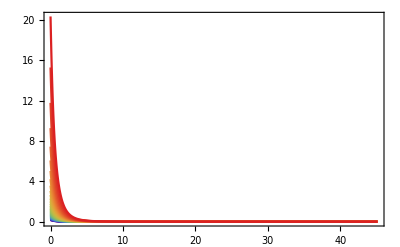

```mathematica
PlotEnvRisk[parameter=α,α,β,κ,μ,w0,Tmax]
```

Effect of β

Evolutionary stable degree of risk aversion across a range of values for the β parameter, which captures the “safeness” of the environment. 
β  > 0 and higher values mean an environment where it is easier to obtain protections against mortality sources.

```mathematica
Clear[β]
α :=0.5
κ:=1
μ:=0.1
w0:=1
Tmax:=70
βmin:=0.025
βmax:=0.25
nc:=50
int=Subdivide[βmin,βmax,nc-1];
params={};
LHSRisk={};
risk={};
```

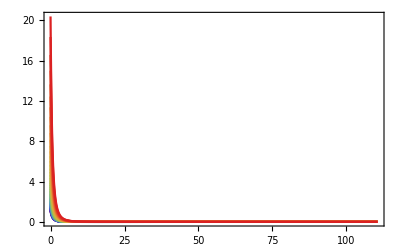

```mathematica
PlotEnvRisk[parameter=β,α,β,κ,μ,w0,Tmax]
```

Effect of w0

Evolutionary stable degree of risk aversion across a range of values for the w0 parameter, which is individuals’ body weight at birth (w0 ≥ 1).

```mathematica
Clear[w0]
α :=0.5;
β:=0.1;
κ:=1;
μ:=0.1;
Tmax:=70;
w0min:=1;
w0max:=20;
nc:=100;
int=Subdivide[w0min,w0max,nc-1];
params={};
LHSRisk={};
risk={};
```

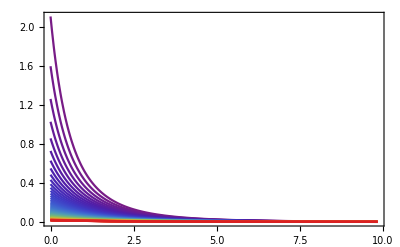

```mathematica
PlotEnvRisk[parameter=w0,α,β,κ,μ,w0,Tmax]
```